## Initialization

```mathematica
Equation:=(u[j,n+1]-u[j,n])/τ==α/h^4 (u[j-2,n]-4 u[j-1,n]+6 u[j,n]-4 u[j+1,n]+u[j+2,n]);
```

```mathematica
U[j_,n_]:=Subscript[U, n]^j
```

```mathematica
u[j_,n_]:=A[n] ⅇ^(ⅈ k j h)
```

```mathematica
sol:=Solve[Equation/.{A[n+1]->β A[n]},β];//FullSimplify
```

```mathematica
ampfac[h_,t_]:=First[β/.sol]//FullSimplify
```

```mathematica
ampfac[x,y]
```

(h^4+6 α τ+2 α τ (-4 Cos[h k]+Cos[2 h k]))/h^4

```mathematica
Assuming[τ>0,Reduce[ampfac[x,y]==1/.α->-1,{h,τ}]]//MatrixForm//FullSimplify
```

h≠0&&((C[1]∈Integers&&(h==(2 π C[1])/k||k==0))||τ==0)

```mathematica
Assuming[τ>0,Reduce[ampfac[x,y]<1/.α->-1,{h,τ}]]//MatrixForm//FullSimplify
```

τ>0&&k==Re[k]&&((Cos[(h k)/2]≠0&&Tan[(h k)/2]≠0&&(h∈Reals||(Re[k]≠0&&((2 h==(π C[2])/Re[k]&&(C[2]≤-1||C[2]≥1)&&(C[2]/2∈Integers||C[2]∈Integers))||(h==(π C[3])/Re[k]&&(C[3]≤-1||C[3]≥1)&&C[3]∈Integers))))&&1/2 (-1+(h k)/π)∉Integers)||(h==(π+2 π C[1])/Re[k]&&Re[k]≠0&&(C[1]≤-1||C[1]≥0)&&C[1]∈Integers))

```mathematica
Reduce[{Cos[(h*k)/2] == 0},h]//FullSimplify
```

C[1]∈Integers&&k≠0&&(h==(π (-1+4 C[1]))/k||h==(π+4 π C[1])/k)

```mathematica
Reduce[{Sin[(h*k)/2] == 0},h]//FullSimplify
```

C[1]∈Integers&&(h==(4 π C[1])/k||h==(2 (π+2 π C[1]))/k||k==0)

```mathematica
f[h_,τ_]:=(h^4-6 τ-2 τ (-4 Cos[h k]+Cos[2 h k]))/h^4
```

```mathematica
f[.1,.1]/.k->.5
```

0.993753

```mathematica
Equation
```

(-ⅇ^(ⅈ h j k) A[n]+ⅇ^(ⅈ h j k) A[1+n])/τ==(α (ⅇ^(ⅈ h (-2+j) k) A[n]-4 ⅇ^(ⅈ h (-1+j) k) A[n]+6 ⅇ^(ⅈ h j k) A[n]-4 ⅇ^(ⅈ h (1+j) k) A[n]+ⅇ^(ⅈ h (2+j) k) A[n]))/h^4

## Calculation

```mathematica
?? EvaluationTimer
```

Information::notfound: Symbol "EvaluationTimer" not found.

```mathematica
FullSimplify[Reduce[f[h,t]≥-1&&f[h,t]≤1/.k->(2 π)/λ,t],λ>0,t>0,h>0]
```

$Aborted

```mathematica
Simplify[Reduce[a x^3≤  1&&a x^3≥-1],a>0]
```

(x<0&&a≥1/x^3&&a+1/x^3≤0)||x==0||(x>0&&a+1/x^3≥0&&a≤1/x^3)

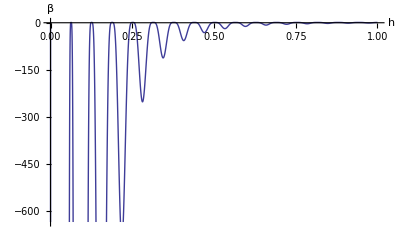

```mathematica
plotFor1=Plot[f[h,.1]/.{k->100},{h,0,1},AxesLabel->{"h","β"}]
```

```mathematica
SetDirectory["/Users/kevin/Skydrive/KTH Work/LaTeX Reports/Stability HW3/Figures/"]
```

/Users/kevin/SkyDrive/KTH Work/LaTeX Reports/Stability HW3/Figures

```mathematica
Export["vonNeumannPlot",plotFor1,"EPS"]
```

vonNeumannPlot2

```mathematica
Simplify[Reduce[(h^4-6 τ-2 τ (-4 Cos[h k]+Cos[2 h k]))/h^4≤1,{h,τ}],τ>0&&k>0&&h>0]//FullSimplify
```

True

```mathematica
Simplify[Reduce[(h^4-6 τ-2 τ (-4 Cos[h k]+Cos[2 h k]))/h^4≥-1,{h,τ}],τ>0&&k>0&&h>0]//FullSimplify
```

Reduce[h^4+4 τ Cos[h k]≥τ (3+Cos[2 h k]),{h,τ}]

```mathematica
Simplify[Reduce[(h^4-6 τ-2 τ (-4 Cos[h k]+Cos[2 h k]))/h^4<-1,{h,τ}],τ>0&&k>0&&h>0]//FullSimplify
```

```mathematica
(C[1]∈Integers&&π+2 π C[1]==h k&&8 k^4 τ>(π+2 π C[1])^4&&(C[1]≤-1||C[1]≥0))||(1/2 (-1+(h k)/π)∉Integers&&Cos[(h k)/2]≠0&&Tan[(h k)/2]≠0&&((C[2]∈Integers&&2 h k==π C[2]&&128 k^4 τ>π^4 C[2]^4 Csc[(h k)/2]^4&&(C[2]≤-1||C[2]≥1))||(C[3]∈Integers&&h k==π C[3]&&8 k^4 τ>π^4 C[3]^4 Csc[(h k)/2]^4&&(C[3]≤-1||C[3]≥1))||8 τ>h^4 Csc[(h k)/2]^4))
```

```mathematica
Simplify[Reduce[1-<-1,{h,τ}],τ>0&&k>0&&h>0]//FullSimplify
```

```mathematica
((-6 τ-2 τ (-4 Cos[h k]+Cos[2 h k]))/h^4)/(τ/h^4)
```

(-6 τ-2 τ (-4 Cos[h k]+Cos[2 h k]))/τ

```mathematica
2^4
```

16

```mathematica
128/16
```

8

## Reference

```mathematica
Equation/.u->U
```

(-U[j,n]+U[j,1+n])/τ==(α (U[-2+j,n]-4 U[-1+j,n]+6 U[j,n]-4 U[1+j,n]+U[2+j,n]))/h^4

```mathematica
Equation/.u->U
```

(-U_n^j+U_(1+n)^j)/τ==(α (U_n^(-2+j)-4 U_n^(-1+j)+6 U_n^j-4 U_n^(1+j)+U_n^(2+j)))/h^4

```mathematica
solution=Solve[Equation,u[j,n+1]]; (* Solve Equation for u(j,n+1) *)
```

```mathematica
First[solution]//TraditionalForm
```

{u(j,n+1)→(h^4 u(j,n)+α τ u(j-2,n)-4 α τ u(j-1,n)+6 α τ u(j,n)-4 α τ u(j+1,n)+α τ u(j+2,n))/h^4}

Assume u(x_j,t^n) is an exponential function, A(t)ⅇ^(ⅈ k x) to solve for the amplification factor

```mathematica
Equation
```

(-u[j,n]+u[j,1+n])/τ==(α (u[-2+j,n]-4 u[-1+j,n]+6 u[j,n]-4 u[1+j,n]+u[2+j,n]))/h^4

```mathematica
Solve[Equation/.{u[j,n]->A[n] ⅇ^(i k j h),α->-1},A[n+1] ⅇ^(i k j h)]//FullSimplify
```

Solve[(-ⅇ^(h i j k) A[n]+u[j,1+n])/τ==-(6 ⅇ^(h i j k) A[n]+u[-2+j,n]-4 (u[-1+j,n]+u[1+j,n])+u[2+j,n])/h^4,ⅇ^(h i j k) A[1+n]]

```mathematica
f[h_,τ_,k_]:=(h^4-6 τ+8 τ Cos[h k]-2 τ Cos[2 h k])/h^4
```

```mathematica
Solve[f[h,τ,2 π/λ]==1,{h,τ}]
```

{{h→-λ},{h→λ},{τ→0}}

```mathematica
f[0,τ,2 π/λ]
```

Indeterminate

```mathematica
Solve[-6 τ+8 τ Cos[h k]-2 τ Cos[2 h k]==0/.k->2 π/λ,{h,τ}]
```

{{h→0},{h→-λ},{h→λ},{τ→0}}